```mathematica
dat75 = Import["/Users/pascalmichel/Desktop/WiSe 16:17/Computersimulation/Projekt/Lennard-Jones-Liquid/Daten/T=0.75/HistogramDensities.txt","Data"];dat85 = Import["/Users/pascalmichel/Desktop/WiSe 16:17/Computersimulation/Projekt/Lennard-Jones-Liquid/Daten/T=0.85/HistogramDensities.txt","Data"];dat95 = Import["/Users/pascalmichel/Desktop/WiSe 16:17/Computersimulation/Projekt/Lennard-Jones-Liquid/Daten/T=0.95/HistogramDensities.txt","Data"];dat105 = Import["/Users/pascalmichel/Desktop/WiSe 16:17/Computersimulation/Projekt/Lennard-Jones-Liquid/Daten/T=1.05/HistogramDensities.txt","Data"];dat106 = Import["/Users/pascalmichel/Desktop/WiSe 16:17/Computersimulation/Projekt/Lennard-Jones-Liquid/Daten/T=1.06/HistogramDensities.txt","Data"];dat107 = Import["/Users/pascalmichel/Desktop/WiSe 16:17/Computersimulation/Projekt/Lennard-Jones-Liquid/Daten/T=1.07/HistogramDensities.txt","Data"];dat108 = Import["/Users/pascalmichel/Desktop/WiSe 16:17/Computersimulation/Projekt/Lennard-Jones-Liquid/Daten/T=1.08/HistogramDensities.txt","Data"];dat109 = Import["/Users/pascalmichel/Desktop/WiSe 16:17/Computersimulation/Projekt/Lennard-Jones-Liquid/Daten/T=1.09/HistogramDensities.txt","Data"];dat110 = Import["/Users/pascalmichel/Desktop/WiSe 16:17/Computersimulation/Projekt/Lennard-Jones-Liquid/Daten/T=1.10/HistogramDensities.txt","Data"];dat111 = Import["/Users/pascalmichel/Desktop/WiSe 16:17/Computersimulation/Projekt/Lennard-Jones-Liquid/Daten/T=1.11/HistogramDensities.txt","Data"];dat112 = Import["/Users/pascalmichel/Desktop/WiSe 16:17/Computersimulation/Projekt/Lennard-Jones-Liquid/Daten/T=1.12/HistogramDensities.txt","Data"];dat115 = Import["/Users/pascalmichel/Desktop/WiSe 16:17/Computersimulation/Projekt/Lennard-Jones-Liquid/Daten/T=1.15/HistogramDensities.txt","Data"];
data75 =Flatten[Delete[dat75,1]];data85 =Flatten[Delete[dat85,1]];data95 =Flatten[Delete[dat95,1]];data105 =Flatten[Delete[dat105,1]];data106 =Flatten[Delete[dat106,1]];data107 =Flatten[Delete[dat107,1]];data108 =Flatten[Delete[dat108,1]];data109 =Flatten[Delete[dat109,1]];data110 =Flatten[Delete[dat110,1]];data111 =Flatten[Delete[dat111,1]];data112 =Flatten[Delete[dat112,1]];data115 =Flatten[Delete[dat115,1]];
```

```mathematica
Histogram[data75,{0.0005},Epilog->First@Plot[10*PDF[NormalDistribution[0.78,0.01],x],{x,-4,4},PlotStyle->Red]];
Histogram[data75,{0.0005},Epilog->First@Plot[23*PDF[NormalDistribution[0.0087,0.0075],x],{x,-4,4},PlotStyle->Blue]];
```

```mathematica
Histogram[data85,{0.0005},Epilog->First@Plot[5.5*PDF[NormalDistribution[0.728,0.01],x],{x,-4,4},PlotStyle->Red]];
Histogram[data85,{0.0005},Epilog->First@Plot[8.3*PDF[NormalDistribution[0.0201,0.0075],x],{x,-4,4},PlotStyle->Blue]];
```

```mathematica
Histogram[data95,{0.0005},Epilog->First@Plot[6*PDF[NormalDistribution[0.671,0.011],x],{x,-4,4},PlotStyle->Red]];
Histogram[data95,{0.0005},Epilog->First@Plot[4.5*PDF[NormalDistribution[0.041,0.0075],x],{x,-4,4},PlotStyle->Blue]];
```

```mathematica
Histogram[data105,{0.0005},Epilog->First@Plot[6*PDF[NormalDistribution[0.595,0.015],x],{x,-4,4},PlotStyle->Red]];
Histogram[data105,{0.0005},Epilog->First@Plot[3.5*PDF[NormalDistribution[0.085,0.013],x],{x,-4,4},PlotStyle->Blue]];
```

```mathematica
Histogram[data106,{0.0005},Epilog->First@Plot[6*PDF[NormalDistribution[0.581,0.015],x],{x,-4,4},PlotStyle->Red]];
Histogram[data106,{0.0005},Epilog->First@Plot[3.5*PDF[NormalDistribution[0.093,0.013],x],{x,-4,4},PlotStyle->Blue]];
```

```mathematica
Histogram[data107,{0.0005},Epilog->First@Plot[6*PDF[NormalDistribution[0.573,0.015],x],{x,-4,4},PlotStyle->Red]];
Histogram[data107,{0.0005},Epilog->First@Plot[3.5*PDF[NormalDistribution[0.0965,0.013],x],{x,-4,4},PlotStyle->Blue]];
```

```mathematica
Histogram[data108,{0.0005},Epilog->First@Plot[6*PDF[NormalDistribution[0.554,0.015],x],{x,-4,4},PlotStyle->Red]];
Histogram[data108,{0.0005},Epilog->First@Plot[2.5*PDF[NormalDistribution[0.12,0.013],x],{x,-4,4},PlotStyle->Blue]];
```

```mathematica
Histogram[data109,{0.0005},Epilog->First@Plot[6*PDF[NormalDistribution[0.559,0.015],x],{x,-4,4},PlotStyle->Red]];
Histogram[data109,{0.0005},Epilog->First@Plot[2.5*PDF[NormalDistribution[0.112,0.013],x],{x,-4,4},PlotStyle->Blue]];
```

```mathematica
Histogram[data110,{0.0005},Epilog->First@Plot[6*PDF[NormalDistribution[0.553,0.015],x],{x,-4,4},PlotStyle->Red]];
Histogram[data110,{0.0005},Epilog->First@Plot[2.5*PDF[NormalDistribution[0.114,0.013],x],{x,-4,4},PlotStyle->Blue]];
```

```mathematica
Histogram[data111,{0.0005},Epilog->First@Plot[5*PDF[NormalDistribution[0.52,0.015],x],{x,-4,4},PlotStyle->Red]];
Histogram[data111,{0.0005},Epilog->First@Plot[2*PDF[NormalDistribution[0.158,0.013],x],{x,-4,4},PlotStyle->Blue]];
```

```mathematica
Histogram[data112,{0.0005},Epilog->First@Plot[5*PDF[NormalDistribution[0.515,0.015],x],{x,-4,4},PlotStyle->Red]];
Histogram[data112,{0.0005},Epilog->First@Plot[2*PDF[NormalDistribution[0.164,0.013],x],{x,-4,4},PlotStyle->Blue]];
```

```mathematica
Histogram[data115,{0.0005},Epilog->First@Plot[5*PDF[NormalDistribution[0.438,0.015],x],{x,-4,4},PlotStyle->Red]];
Histogram[data115,{0.0005},Epilog->First@Plot[3*PDF[NormalDistribution[0.325,0.013],x],{x,-4,4},PlotStyle->Blue]];
```

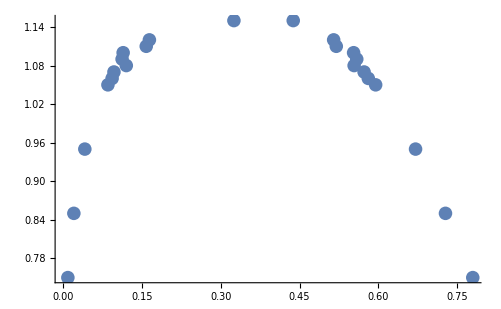

```mathematica
ListPlot[{{0.0087,0.75},{0.78,0.75},{0.0201,0.85},{0.728,0.85},{0.041,0.95},{0.671,0.95},{0.085,1.05},{0.595,1.05},{0.093,1.06},{0.581,1.06},{0.0965,1.07},{0.573,1.07},{0.12,1.08},{0.554,1.08},{0.112,1.09},{0.559,1.09},{0.114,1.10},{0.553,1.10},{0.158,1.11},{0.52,1.11},{0.164,1.12},{0.515,1.12},{0.325,1.15},{0.438,1.15}}]
```